## Dunaev Viktor, 3 kurs, 6 group, 23 variant

## Pre - Task

```mathematica
fname = NotebookDirectory[]<>"input.txt"
```

C:\6_Cemestr\DS_Laguto\input.txt

```mathematica
stream = OpenRead[fname];
```

```mathematica
vertexNum = Read[stream, {Word, Number}]⟦2⟧
```

6

```mathematica
edgesNum =Read[stream, {Word, Number}]⟦2⟧
```

12

```mathematica
edges =Table[#⟦1⟧->#⟦2⟧&[ToExpression[Read[stream]]],edgesNum]
```

{1->5,2->5,3->1,3->4,3->5,4->1,4->2,4->6,5->4,6->2,6->3,6->5}

```mathematica
vertex = Table[i,{i,1,vertexNum}]
```

{1,2,3,4,5,6}

```mathematica
weight = Range[vertexNum]
```

{1,2,3,4,5,6}

```mathematica
Table[(pos = ToExpression[Characters[#⟦1⟧]⟦5⟧];val = #⟦2⟧;weight⟦pos⟧ = val)&[Read[stream, {Word, Number}]],vertexNum]
```

{7,4,-1,-7,-2,-1}

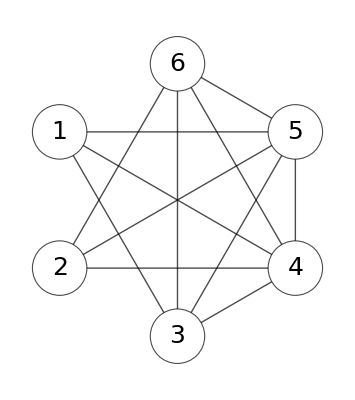

```mathematica
g =Graph[vertex,edges,VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"CircularEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

## Task 1

```mathematica
(*    1) Реализовать функцию пользователя построения характеристических векторов.
2) Вывести покрывающее дерево графа с циклами,порожденными дугами множества Un (см.пример).
  3) Вычислить характеристические вектора,порожденные дугами множества Un.Компоненты веторов вывести в виде таблицы (см.пример) *)
```

```mathematica
startNode = RandomChoice[vertex]
```

6

```mathematica
dirs= Table[0,Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
pred = Table[0, Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
depth = Table[0 , Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
dinast = {}
```

{}

```mathematica
tree = {}
```

{}

```mathematica
graphTree = {}
```

{}

```mathematica
DepthFirstScan[UndirectedGraph@g,startNode,{"FrontierEdge"->((edge =#/.(x_<->y_)->(x->y); AppendTo[tree,edge];If[MemberQ[edges,edge],dirs⟦#⟦2⟧⟧=1;AppendTo[graphTree,edge],dirs⟦#⟦2⟧⟧=-1;AppendTo[graphTree,#⟦2⟧->#⟦1⟧]];pred⟦#⟦2⟧⟧=#⟦1⟧;depth⟦#⟦2⟧⟧ = depth⟦#⟦1⟧⟧+1)&),"PrevisitVertex"->((AppendTo[dinast,#])&)}]
```

{3,5,4,6,1,6}

```mathematica
tree
```

{6->4,4->3,3->1,1->5,5->2}

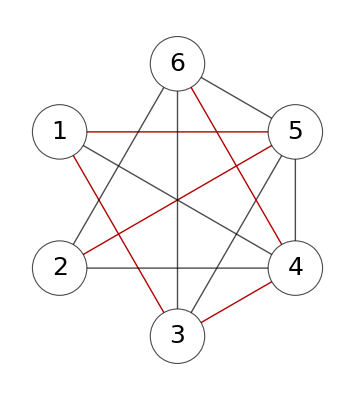

```mathematica
HighlightGraph[g,graphTree]
```

```mathematica
dirs
```

{1,-1,-1,-1,1,0}

```mathematica
pred
```

{3,5,4,6,1,0}

```mathematica
dinast
```

{6,4,3,1,5,2}

```mathematica
depth
```

{3,5,2,1,4,0}

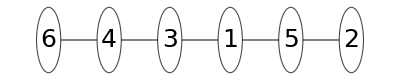

```mathematica
Graph[tree, VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"RadialEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

```mathematica
TableForm[{vertex,pred,depth, dirs},TableHeadings->{{"Вершины","Список предков","Список глубин", "Список направлений"}}]
```

Вершины | 1 | 2 | 3 | 4 | 5 | 6
Список предков | 3 | 5 | 4 | 6 | 1 | 0
Список глубин | 3 | 5 | 2 | 1 | 4 | 0
Список направлений | 1 | -1 | -1 | -1 | 1 | 0

```mathematica
xp = Table[0,Length[vertex] ];
```

```mathematica
For[n = Length[vertex],n>1,n--,
i = dinast⟦n⟧;
xp⟦i⟧+= dirs⟦i⟧*weight⟦i⟧;
xp⟦pred⟦i⟧⟧+= dirs⟦i⟧*dirs⟦pred⟦i⟧⟧*xp⟦i⟧;
]
```

```mathematica
xp
```

{9,-4,-8,-1,2,0}

```mathematica
Un=Select[edges,Not[MemberQ[graphTree,#]]&]
```

{3->5,4->1,4->2,5->4,6->2,6->3,6->5}

```mathematica
Ut=graphTree
```

{4->6,3->4,3->1,1->5,2->5}

```mathematica
table = Table[0,Length[Un],edgesNum];
```

```mathematica
edgesSet= Join[Un,Ut]
```

{3->5,4->1,4->2,5->4,6->2,6->3,6->5,4->6,3->4,3->1,1->5,2->5}

```mathematica
graphs = {};
```

```mathematica
For[i=1,i≤ Length[Un],i++,
τ = Un⟦i⟧⟦1⟧;
ρ=  Un⟦i⟧⟦2⟧;
δ = 0;
AppendTo[graphs,Graph[Join[Ut,{τ->ρ}],GraphHighlight->{τ->ρ},GraphHighlight->{τ->ρ},VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"CircularEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]];
table⟦i⟧⟦i⟧=1;
If[depth⟦τ⟧>depth⟦ρ⟧,δ=1,τ=Un⟦i⟧⟦2⟧;ρ=  Un⟦i⟧⟦1⟧;δ=-1];
depthDelta = depth⟦τ⟧-depth⟦ρ⟧;
For[j=0,j<depthDelta,j++,
ver= pred⟦τ⟧;
If[dirs⟦τ⟧>0,rib = ver->τ,rib = τ->ver];
pos = Position[edgesSet,rib]⟦1⟧;
table⟦i⟧⟦pos⟧=dirs⟦τ⟧*δ;
τ = ver;
];
If[τ≠ ρ,
While[True,
predT = pred⟦τ⟧;
predRho = pred⟦ρ⟧;
If[dirs⟦τ⟧>0,ribT = predT->τ,ribT = τ->predT];
If[dirs⟦ρ⟧>0,ribRho = predRho->ρ,ribRho = ρ->predRho];
posT = Position[edgesSet,ribT]⟦1⟧;
table⟦i⟧⟦posT⟧=dirs⟦τ⟧*δ;
posRho = Position[edgesSet,ribRho]⟦1⟧;
table⟦i⟧⟦posRho⟧=dirs⟦ρ⟧*δ*-1;
τ = predT;
ρ = predRho;
If[τ== ρ,Break[]]
]
]
]
```

```mathematica
TableForm[table,TableHeadings->{Un,edgesSet}]
```

| 3->5 | 4->1 | 4->2 | 5->4 | 6->2 | 6->3 | 6->5 | 4->6 | 3->4 | 3->1 | 1->5 | 2->5
3->5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
4->1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0
4->2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1
5->4 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | 0
6->2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1 | -1 | 1
6->3 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0
6->5 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | -1 | -1 | 0

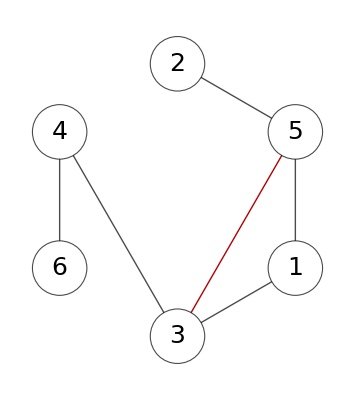
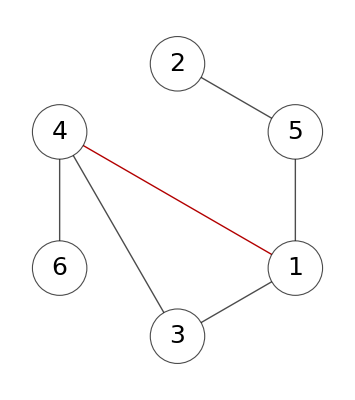
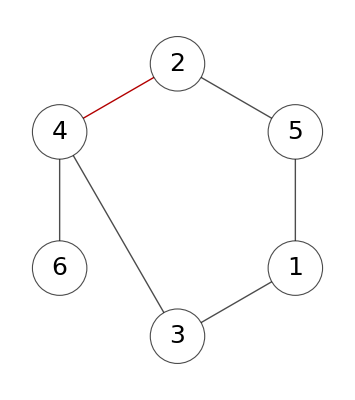
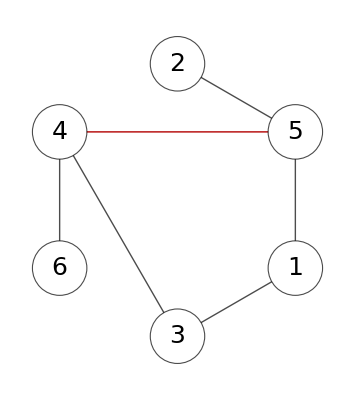
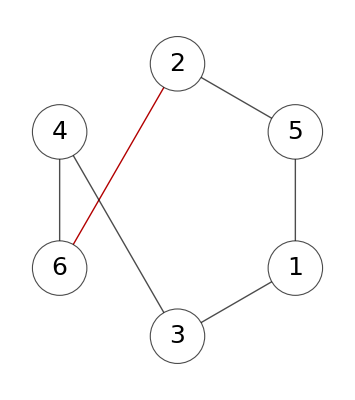
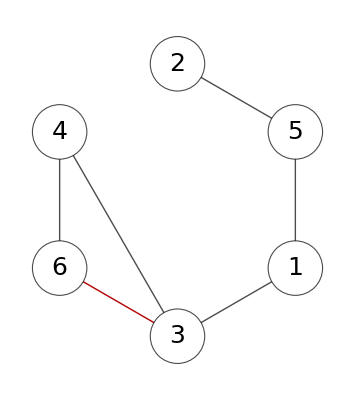
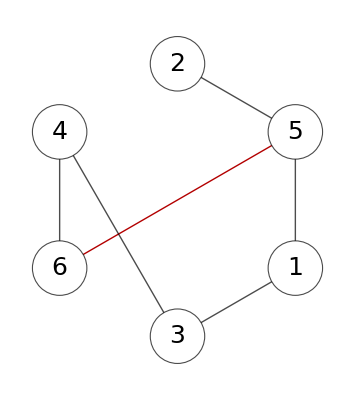

```mathematica
graphs
```